## Uniform

```mathematica
t=0.2;W=05;K=8; v=0.173948268172;x=0;
fn[t_,W_]:=RandomReal[{W,W+0t},K]  (*No more a random list*);
fn2[t_,W_]:=RandomReal[{t,t},K]  (*No more a random list*);
g = fn[t,W];
g2 = fn2[t,W];
g3 = fn2[t,W];
Ox = Table[0,{x,2K},{y,2K}]; 
i=1;While[i<K+1,{Ox[[i,i+K]] = g[[i]],Ox[[i+K,i]] = g[[i]] };i++];
i=1;While[i<K,{Ox[[i+1,i+K]] = Ox[[i+K,i+1]]=g2[[i]]};i++];
i=1;While[i<K,{Ox[[i,i+1+K]] = Ox[[i+K+1,i]]=g2[[i]]};i++];
(* No last and first site connection*)
mat=Ox[[1;;K,K+1;;2K]]
ee2=Eigenvalues[mat];
```

(5. | 0.2 | 0 | 0 | 0 | 0 | 0 | 0
0.2 | 5. | 0.2 | 0 | 0 | 0 | 0 | 0
0 | 0.2 | 5. | 0.2 | 0 | 0 | 0 | 0
0 | 0 | 0.2 | 5. | 0.2 | 0 | 0 | 0
0 | 0 | 0 | 0.2 | 5. | 0.2 | 0 | 0
0 | 0 | 0 | 0 | 0.2 | 5. | 0.2 | 0
0 | 0 | 0 | 0 | 0 | 0.2 | 5. | 0.2
0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 5.)

```mathematica
ee2
```

{5.37588,5.30642,5.2,5.06946,4.93054,4.8,4.69358,4.62412}

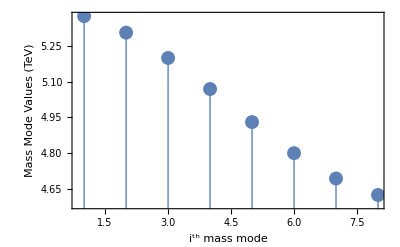

```mathematica
data=Abs[ee2];
plot=ListPlot[data,PlotStyle->PointSize[0.025],PlotRange->All,Frame->True,FrameTicks->{Automatic,Automatic},FrameLabel->{Style[Row[{"\!\(\*SuperscriptBox[\(i\), \(th\)]\)"," mass mode"}],16],Style["Mass Mode Values (TeV)",15]},FrameTicksStyle->Directive[Black,FontSize->14],LabelStyle->Directive[Black,Medium],FrameStyle->Directive[Black]];

pointColor=Cases[plot,{___,Directive[color_,___],___}:>color,Infinity][[1]];

lines=Table[Line[{{i,0},{i,data[[i]]}}],{i,Length[data]}];

Show[plot,Epilog->{Directive[pointColor],lines}]
```

## Randomness

```mathematica
ntt=20000;
```

```mathematica
DistMass= ParallelTable[t=0.2;W=05;K=8; v=0.173948268172;x=0;
fn[t_,W_]:=RandomReal[{0t-2W,2W+0t},K]  (*No more a random list*);
fn2[t_,W_]:=RandomReal[{t,t},K]  (*No more a random list*);
g = fn[t,W];
g2 = fn2[t,W];
g3 = fn2[t,W];
Ox = Table[0,{x,2K},{y,2K}]; 
i=1;While[i<K+1,{Ox[[i,i+K]] = g[[i]],Ox[[i+K,i]] = g[[i]] };i++];
i=1;While[i<K,{Ox[[i+1,i+K]] = Ox[[i+K,i+1]]=0.01^0*g2[[i]]};i++];
i=1;While[i<K,{Ox[[i,i+1+K]] = Ox[[i+K+1,i]]=0.01^0*g2[[i]]};i++];
(* No last and first site connection*)
mat=Ox[[1;;K,K+1;;2K]];
ee2=Eigenvalues[mat];
ee=SingularValueDecomposition[mat][[2]]//Diagonal;
ev=Eigenvectors[mat];ee,{val,1,ntt}];
```

```mathematica
DistMass[[1]]
```

{9.79312,8.00716,7.89521,5.03086,2.72659,2.32517,0.958912,0.233285}

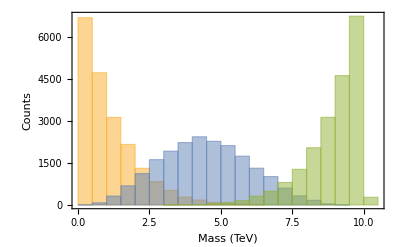

```mathematica
Histogram[{Table[DistMass[[i,-1]],{i,1,ntt}],Table[DistMass[[i,5]],{i,1,ntt}],Table[DistMass[[i,1]],{i,1,ntt}]},PlotRange->All,Frame->True,FrameLabel->{"Mass (TeV)","Counts"},BaseStyle->{FontSize->14,FontWeight->"Bold",FontColor->Darker[Black]}]
```

## Modes

## Local

```mathematica
t=0.20;W=05;K=8; v=0.173948268172;x=0;c=1.2;
```

```mathematica
fn[t_,W_]:=RandomReal[{-2W+0t,2W+0t},K]  (*No more a random list*)
fn2[t_,W_]:=RandomReal[{t,t+x*t},K]  (*No more a random list*)
```

```mathematica
g = fn[t,W];
g2 = fn2[t,W];
g3 = fn2[t,W];
```

```mathematica
Ox = Table[0,{x,2K},{y,2K}];
```

```mathematica
i=1;While[i<K+1,{Ox[[i,i+K]] = g[[i]],Ox[[i+K,i]] = g[[i]] };i++]
i=1;While[i<K,{Ox[[i+1,i+K]] = Ox[[i+K,i+1]]=0.01^0*g2[[i]]};i++]
i=1;While[i<K,{Ox[[i,i+1+K]] = Ox[[i+K+1,i]]=0.01^0*g2[[i]]};i++]
(* No last and first site connection*)
```

```mathematica
Ox;
```

```mathematica
mat=Ox[[1;;K,K+1;;2K]]
```

(1.96146 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0
0.2 | -6.07109 | 0.2 | 0 | 0 | 0 | 0 | 0
0 | 0.2 | -2.5042 | 0.2 | 0 | 0 | 0 | 0
0 | 0 | 0.2 | -9.76765 | 0.2 | 0 | 0 | 0
0 | 0 | 0 | 0.2 | 3.22386 | 0.2 | 0 | 0
0 | 0 | 0 | 0 | 0.2 | 6.56095 | 0.2 | 0
0 | 0 | 0 | 0 | 0 | 0.2 | 3.96418 | 0.2
0 | 0 | 0 | 0 | 0 | 0 | 0.2 | -3.19444)

```mathematica
ee=Eigenvalues[mat]
```

{-9.77624,6.58812,-6.08719,3.95475,3.21479,-3.20003,-2.48758,1.96644}

```mathematica
ee=SingularValueDecomposition[mat][[2]]//Diagonal
```

{9.77624,6.58812,6.08719,3.95475,3.21479,3.20003,2.48758,1.96644}

```mathematica
ev=Eigenvectors[mat];
```

```mathematica
Min[Abs[ev[[-1]]]]
```

5.12885×10^-10

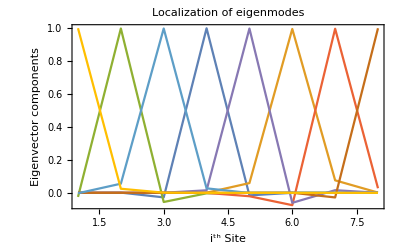

```mathematica
ListLinePlot[Table[ev[[i]],{i,1,K}],PlotRange->All,Frame->True,PlotLabel->Style["Localization of eigenmodes",Black,16],LabelStyle->Directive[Black],FrameTicks->{Automatic,Automatic},FrameLabel->{Style[Row[{"i^th Site"}],15],Style["Eigenvector components",14]},FrameTicksStyle->Directive[Black,FontSize->14],AxesOrigin->{1,None},InterpolationOrder->1]
```

```mathematica
{um,wm,vm}=SingularValueDecomposition[mat];
```

```mathematica
um
```

(-0.000025344 | 1.08917×10^-8 | -0.0248027 | -1.8645×10^-8 | 1.85654×10^-6 | -4.07851×10^-10 | -0.00249781 | -0.999689
0.0014874 | 2.51961×10^-7 | 0.998143 | -1.85824×10^-7 | 0.0000116343 | 1.05256×10^-8 | 0.0555644 | -0.0249033
-0.0275298 | 0.0000159372 | -0.0555474 | -9.29658×10^-6 | 0.000538319 | 1.51506×10^-7 | 0.998076 | -0.00111493
0.999502 | 0.00072428 | -0.00301498 | -0.000300045 | 0.0153816 | -5.37637×10^-7 | 0.027393 | -0.0000189515
-0.0153797 | 0.0592149 | 0.0000647834 | -0.0205774 | 0.997914 | -0.0000178065 | -0.000959977 | 3.03546×10^-6
0.000188312 | 0.995348 | -1.02472×10^-6 | -0.0748991 | -0.0606041 | 0.000572472 | 0.0000212328 | -1.3271×10^-7
-2.74221×10^-6 | 0.0759852 | 2.04177×10^-8 | 0.996589 | 0.0160407 | -0.0279216 | -6.52479×10^-7 | 1.32347×10^-8
8.33272×10^-8 | 0.00155348 | -1.41164×10^-9 | 0.0278798 | 0.000500548 | 0.99961 | -1.84612×10^-7 | 5.12885×10^-10)

```mathematica
Iev=Inverse[ev];
```

```mathematica
v1=v*um[[1]];
vn=1*um[[-1]];
```

```mathematica
mm=Table[0,{i,K+1},{j,K+1}];
```

```mathematica
i=1;While[i<K+1,{mm[[i+1,i+1]]=ee[[i]]};i++]
i=1;While[i<K+1,{mm[[1,i+1]]=v1[[i]];mm[[i+1,1]]=vn[[i]]};i++]
```

```mathematica
mm
```

(0 | -4.40854×10^-6 | 1.89459×10^-9 | -0.00431439 | -3.24327×10^-9 | 3.22942×10^-7 | -7.09451×10^-11 | -0.00043449 | -0.173894
8.33272×10^-8 | 9.77624 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.00155348 | 0 | 6.58812 | 0 | 0 | 0 | 0 | 0 | 0
-1.41164×10^-9 | 0 | 0 | 6.08719 | 0 | 0 | 0 | 0 | 0
0.0278798 | 0 | 0 | 0 | 3.95475 | 0 | 0 | 0 | 0
0.000500548 | 0 | 0 | 0 | 0 | 3.21479 | 0 | 0 | 0
0.99961 | 0 | 0 | 0 | 0 | 0 | 3.20003 | 0 | 0
-1.84612×10^-7 | 0 | 0 | 0 | 0 | 0 | 0 | 2.48758 | 0
5.12885×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.96644)

```mathematica
Eigenvalues[mm]
```

{9.77624,6.58812,6.08719,3.95475,3.21479,3.20003,2.48758,1.96644,6.44462×10^-12}

```mathematica
SingularValueDecomposition[mm][[2]]//Diagonal
```

{9.77624,6.58812,6.08719,3.95487,3.3525,3.21479,2.48758,1.97412,6.12585×10^-12}

## Nonlocal

```mathematica
t=0.25;W=05;K=8; v=0.173948268172;x=0;c=2;
```

```mathematica
fn[t_,W_]:=RandomReal[{-2W-0t,2W+0t},K]  (*No more a random list*)
fn2[t_,W_]:=RandomReal[{t,t+x*t},K]  (*No more a random list*)
```

```mathematica
g = fn[t,W];
g2 = fn2[t,W];
g3 = fn2[t,W];
```

```mathematica
Ox = Table[0,{x,2K},{y,2K}];
```

```mathematica
i=1;
While[i<K+1,{j=1;
While[j<K+1,{Ox[[i,j+K]] = c*g2[[i]]/Power[c,Abs[i-j]],Ox[[j+K,i]] = c*g2[[i]]/Power[c,Abs[i-j]]};j++]};i++]
i=1;While[i<K+1,{Ox[[i,i+K]] = g[[i]],Ox[[i+K,i]] = g[[i]] };i++](*Exponentially decaying hopping terms*)
```

```mathematica
Ox;
```

```mathematica
mat=Ox[[1;;K,K+1;;2K]];
```

```mathematica
mat=(mat+Transpose[mat])/2;
```

```mathematica
ee=Eigenvalues[mat]
```

{9.31721,9.17029,-6.68576,-5.66581,4.50409,3.66479,-1.9356,0.87787}

```mathematica
ee=SingularValueDecomposition[mat][[2]]//Diagonal
```

{9.31721,9.17029,6.68576,5.66581,4.50409,3.66479,1.9356,0.87787}

```mathematica
ev=Eigenvectors[mat];
```

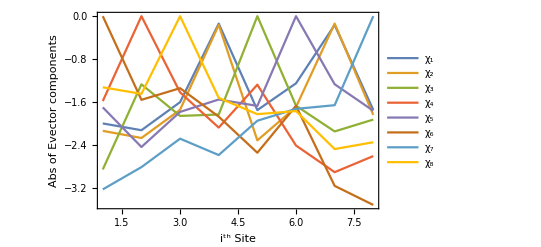

```mathematica
ListLinePlot[Log10[Abs[Table[ev[[i]],{i,1,K}]]],PlotRange->All,Frame->True,PlotLabel->Style["",Black,16],LabelStyle->Directive[Black],FrameLabel->{Style[Row[{"i^th Site"}],15],Style["Abs of Evector components",14]},FrameTicksStyle->Directive[Black,FontSize->14],AxesOrigin->{1,None},PlotRange->{{1,7},Automatic},InterpolationOrder->1,PlotLegends->{"χ_1","χ_2","χ_3","χ_4","χ_5","χ_6","χ_7","χ_8"}]
```

```mathematica
{um,wm,vm}=SingularValueDecomposition[mat];
```

```mathematica
um;
```

```mathematica
Iev=Inverse[ev];
```

```mathematica
v1=v*um[[1]];
vn=v*um[[-1]];
```

```mathematica
mm=Table[0,{i,K+1},{j,K+1}];
```

```mathematica
i=1;While[i<K+1,{mm[[i+1,i+1]]=ee[[i]]};i++]
i=1;While[i<K+1,{mm[[1,i+1]]=v1[[i]];mm[[i+1,1]]=vn[[i]]};i++]
```

```mathematica
mm
```

(0 | -0.0478769 | 0.000357484 | -0.00285466 | 0.0751295 | -0.0363247 | 0.0999496 | -0.0879391 | 0.0195014 | -0.0234319 | -0.0237486 | 0.0395121 | -0.0146911
-0.00732448 | 36.5187 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.044141 | 0 | 10.2156 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.0115922 | 0 | 0 | 9.8541 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.00914945 | 0 | 0 | 0 | 8.9956 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.00736083 | 0 | 0 | 0 | 0 | 8.52084 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.0116888 | 0 | 0 | 0 | 0 | 0 | 7.4661 | 0 | 0 | 0 | 0 | 0 | 0
0.00777129 | 0 | 0 | 0 | 0 | 0 | 0 | 6.75201 | 0 | 0 | 0 | 0 | 0
0.0549677 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.60793 | 0 | 0 | 0 | 0
0.0906774 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.8312 | 0 | 0 | 0
-0.00808849 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.02011 | 0 | 0
0.0378981 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.49269 | 0
-0.122642 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.583886)

```mathematica
Eigenvalues[mm]
```

{36.5187,10.2156,9.8541,8.99552,8.52081,7.46594,6.7519,5.60813,2.83045,2.02021,1.49369,0.586952,-0.00325214}

```mathematica
SingularValueDecomposition[mm][[2]]//Diagonal
```

{36.5187,10.2157,9.8541,8.99592,8.52092,7.46677,6.75258,5.60824,2.83275,2.02027,1.4937,0.596774,0.00319496}

## Petersen

```mathematica
t=0.25;W=05;K=8; v=0.173948268172;x=0;c=2;
```

```mathematica
fn[t_,W_]:=RandomReal[{-2W-0t,2W+0t},K]  (*No more a random list*)
fn2[t_,W_]:=RandomReal[{t,t+x*t},2K]  (*No more a random list*)
```

```mathematica
g = fn[t,W];
g2 = fn2[t,W];
g3 = fn2[t,W];
```

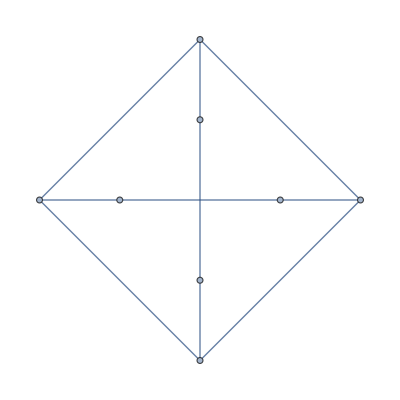

```mathematica
p =PetersenGraph[K/2,K/4,EdgeStyle->Thick]
```

```mathematica
mat = WeightedAdjacencyMatrix[p]
```

SparseArray[…]

```mathematica
i=1;
While[i<K+1,{mat[[i,i]]=g[[i]]};i++]
```

```mathematica
i=1;
While[i<K+1,{j=1;
While[j<K+1,{If[i==j,mat[[i,j]]=mat[[i,j]],mat[[i,j]]=c*g2[[i+j]]*mat[[i,j]]/Power[c,Abs[i-j]]]};j++]};i++]
```

```mathematica
mat=mat//Normal
```

(-0.56962 | 0 | 0.125 | 0 | 0.03125 | 0 | 0 | 0
0 | -9.50949 | 0 | 0.125 | 0 | 0.03125 | 0 | 0
0.125 | 0 | 9.00119 | 0 | 0 | 0 | 0.03125 | 0
0 | 0.125 | 0 | 3.33898 | 0 | 0 | 0 | 0.03125
0.03125 | 0 | 0 | 0 | 9.66613 | 0.25 | 0 | 0.0625
0 | 0.03125 | 0 | 0 | 0.25 | -3.51671 | 0.25 | 0
0 | 0 | 0.03125 | 0 | 0 | 0.25 | -5.51366 | 0.25
0 | 0 | 0 | 0.03125 | 0.0625 | 0 | 0.25 | 6.27086)

```mathematica
ee=SingularValueDecomposition[mat][[2]]//Diagonal
```

{9.67212,9.51087,9.00289,6.27534,5.54982,3.4905,3.33986,0.571348}

```mathematica
ev=Eigenvectors[mat];
```

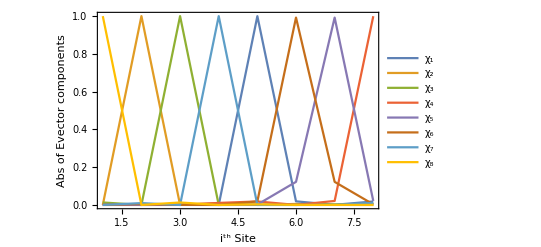

```mathematica
ListLinePlot[Abs[Table[ev[[i]],{i,1,K}]],PlotRange->All,Frame->True,PlotLabel->Style["",Black],FrameLabel->{Style[Row[{"i^th Site"}],16],Style["Abs of Evector components",16]},LabelStyle->Directive[Black],FrameTicks->{Automatic,Automatic},FrameTicksStyle->Directive[Black,FontSize->16],AxesOrigin->{1,None},PlotRange->{{1,7},Automatic},InterpolationOrder->1,PlotLegends->{"χ_1","χ_2","χ_3","χ_4","χ_5","χ_6","χ_7","χ_8"}]
```

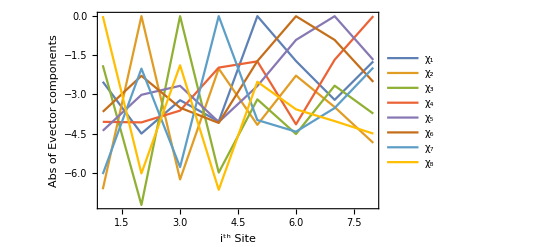

```mathematica
ListLinePlot[Log10[Abs[Table[ev[[i]],{i,1,K}]]],PlotRange->All,Frame->True,PlotLabel->Style["",Black],FrameLabel->{Style[Row[{"i^th Site"}],16],Style["Abs of Evector components",16]},LabelStyle->Directive[Black],FrameTicks->{Automatic,Automatic},FrameTicksStyle->Directive[Black,FontSize->16],AxesOrigin->{1,None},PlotRange->{{1,7},Automatic},InterpolationOrder->1,PlotLegends->{"χ_1","χ_2","χ_3","χ_4","χ_5","χ_6","χ_7","χ_8"}]
```

```mathematica
{um,wm,vm}=SingularValueDecomposition[mat];
```

```mathematica
um;
```

```mathematica
Iev=Inverse[ev];
```

```mathematica
v1=v*um[[1]];
vn=1*um[[-1]];
```

```mathematica
mm=Table[0,{i,K+1},{j,K+1}];
```

```mathematica
i=1;While[i<K+1,{mm[[i+1,i+1]]=ee[[i]]};i++]
i=1;While[i<K+1,{mm[[1,i+1]]=v1[[i]];mm[[i+1,1]]=vn[[i]]};i++]
```

```mathematica
mm;
```

```mathematica
ev1=SingularValueDecomposition[mm][[2]]//Diagonal
```

{13.2346,12.7346,7.72193,7.22169,4.86563,4.36572,3.17665,2.67692,2.18919,1.69067,0.646621,0.250665,0.0830512}

```mathematica
svd=SingularValueDecomposition[mm];
```

## L vs NL vs Petersen

```mathematica
nt=50000;
```

```mathematica
t1=AbsoluteTime[];
pt=ParallelTable[t=0.25;c=2;W=5;K=12;l=t*c;
fn[t_,W_]:=RandomReal[{W- W/2,W+W/2},K]  ;
g = fn[t,W];
Ox = Table[0,{x,2K+1},{y,2K+1}]; 
i=1;While[i<K+1,{Ox[[i,i+K]] = g[[i]],Ox[[i+K,i]] = g[[i]] };i++];
i=1;While[i<K,{Ox[[i+1,i+K]] = t,Ox[[i+K,i+1]]=t};i++];
i=1;While[i<K,{Ox[[i,i+1+K]] = t ,Ox[[i+K+1,i]]=t};i++];
Ox[[2K+1,1]]=t;Ox[[1,2K+1]] = t; Ox[[2K+1,2K+1]] = W;
Ox;
ml=Ox[[1;;K,K+1;;2K]];
Ox = Table[0,{x,2K+1},{y,2K+1}]; 
Ox[[2K+1,1]]=l/c;Ox[[1,2K+1]] = l/c; Ox[[2K+1,2K+1]] = W;
i=1;
While[i<K+1,{j=1;
While[j<K+1,{Ox[[i,j+K]] = l/Power[c,Abs[i-j]],Ox[[j+K,i]] = l/Power[c,Abs[i-j]]};j++]};i++];
i=1;While[i<K+1,{Ox[[i,i+K]] = g[[i]],Ox[[i+K,i]] = g[[i]] };i++](*Exponentially decaying hopping terms*);
Ox;
mnl=Ox[[1;;K,K+1;;2K]];
p =PetersenGraph[K/2,K/4,EdgeStyle->Thick];
mat = WeightedAdjacencyMatrix[p];
i=1;
While[i<K+1,{mat[[i,i]]=g[[i]]};i++];
i=1;
While[i<K+1,{j=1;
While[j<K+1,{If[i==j,mat[[i,j]]=mat[[i,j]],mat[[i,j]]=l*mat[[i,j]]/Power[c,Abs[i-j]]]};j++]};i++];
mpet=Normal[mat];
Eigenvalues[ml];
Eigenvalues[mnl];
Eigenvalues[mpet];
ec1=Eigenvectors[ml];
ec2=Eigenvectors[mnl];
ec3=Eigenvectors[mpet];
Min[Abs[ec1]];
Min[Abs[ec2]];
Min[Abs[ec3]];ci=-12;
e1=ec1[[ci]];
e2=ec2[[ci]];
e3=ec3[[ci]];
{Min[Abs[e1]],
Min[Abs[e2]],
Min[Abs[e3]]},{i,1,nt}];
AbsoluteTime[]-t1
```

12.2767

```mathematica
Length[pt]
```

50000

```mathematica
pt[[1]]
```

{1.36228×10^-9,0.00220578,0.0000814456}

```mathematica
subsetsOf10=Partition[pt,50];
```

```mathematica
subsetsOf10;
```

```mathematica
medians=Median/@subsetsOf10;
```

```mathematica
medians[[1]]
```

{2.27404×10^-7,0.00783765,9.31414×10^-6}

```mathematica
medians[[;;,1]];
```

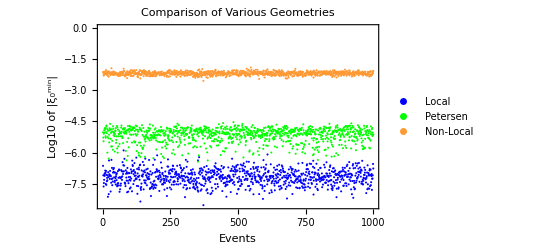

```mathematica
ListPlot[{Log10[medians[[;;,1]]],Log10[medians[[;;,3]]],Log10[medians[[;;,2]]]},PlotLegends->{Style["Local",Black,12],Style["Petersen",Black,12],Style["Non-Local",Black,12]},PlotStyle->{Blue,Green, RGBColor[255/255,153/255,51/255]},PlotLabel->Style["Comparison of Various Geometries",Black,16],Frame->True,FrameTicksStyle->Directive[Black,FontSize->14],FrameLabel->{Style["Events",Black,16],Style["Log10 of |ξ_0^min|",Black,16]}]
```

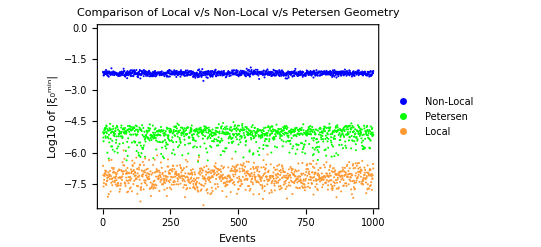

```mathematica
ListPlot[{Log10[medians[[;;,2]]],Log10[medians[[;;,3]]],Log10[medians[[;;,1]]]},PlotLegends->{Style["Non-Local",Black,12],Style["Petersen",Black,12],Style["Local",Black,12]},PlotStyle->{Blue,Green, RGBColor[255/255,153/255,51/255]},PlotLabel->Style["Comparison of Local v/s Non-Local v/s Petersen Geometry",Black,10],Frame->True,FrameLabel->{Style["Events",Black,10],Style["Log10 of |ξ_0^min|",Black,10]}]
```